```mathematica
SetOptions[EvaluationNotebook[],AutoGeneratedPackage->Automatic]
```

## Euclidean highest common factor

## Winding number

```mathematica
euclideanQCoefficients[{m_,n_}] := Module[{r,q,i},
	i=0;
	r[-1]=n; 
	r[0] = m;
	While[r[i] > 0  , 
		q[i] = Floor[r[i-1]/r[i]];
		r[i+1] = r[i-1] - q[i]*r[i];
		i++;
	];
 Table[q[j],{j,0,i-1}]
];
(* 
euclideanQCoefficients[{0,1}] := {}; 
euclideanQCoefficients[{1,0}] := {0}; 
*)
```

```mathematica
(* need one of m and n > 0;  creates a matrix with ({{m, u}, {n, v}})  and | m v -  nu |=1, no assumption that m<n*)
```

```mathematica
eMatrix = ({{1, 1}, {0, 1}});sMatrix=({{0, 1}, {1, 0}});

euclideanMatrixProduct[mn_] := Module[{q,res},
q = euclideanQCoefficients[mn];
res= (Map[  MatrixPower[eMatrix,#]. sMatrix &,q]);
res= If[Length[res]>0,Dot@@res,IdentityMatrix[2]];
res = sMatrix . res;

res
]/; NumericQ[First[mn]];
euclideanMatrixProduct[{1,0}] = ({{0, -1}, {1, 0}});
euclideanMatrixProduct[{0,1}] = ({{1, 0}, {0, -1}});
euclideanDelta[mn_]  := Det@euclideanMatrixProduct[mn];

euclideanMatrixProductNew[mn_] := sMatrix. euclideanMatrixProduct[mn]

euclideanMatrixProductNew[{1,0}] = ({{0, -1}, {1, 0}});
euclideanMatrixProductNew[{0,1}] = ({{1, 0}, {0, -1}});
```

```mathematica
(* requires m & n >= 0 *)
euclideanHighestCommonFactor[mn_] := Module[{res},
res =  Inverse[euclideanMatrixProduct[mn]]  .  mn ;  
If[res[[2]] !=0 , Abort[]];
First[res]
];

euclideanWindingNumberPair[mn_] := Module[{m,n,u,v},
{{m,u},{n,v}}= euclideanMatrixProduct[mn];
{u,v}
];
(*euclideanWindingNumberPairNew[mn_] := Module[{m,n,u,v},
{{m,u},{n,v}}= euclideanMatrixProductNew[mn];
{u,v}
];
*)
euclideanFareyInterval[{0,1}] = {0,1/2};
euclideanFareyInterval[{1,0}] = {0,1/2};
euclideanFareyInterval[{1,1}] = {0,1/2}; 

euclideanFareyInterval[{m_,n_}] := Module[{u,v,delta,interval},
{u,v} = euclideanWindingNumberPair[{m,n}];
delta = euclideanDelta[{m,n}];
interval =  {u/m,v/n};
If[delta <0, interval=Reverse@interval];
interval
];
```

## Mobius maps

### gmn map

```mathematica
basisChangeMatrix[mn_] := Transpose[({{1, 0}, {0, -1}}) .Transpose[ euclideanMatrixProductNew[mn]]];
basisInverseChangeMatrix[mn_] := Inverse[basisChangeMatrix[mn]];
Clear[n,m,v,u];
basisChangeMatrix[{n,m}] := ({{n, -v}, {m, -u}})

matrixToMoebius[matrix_] := Function[z, Divide@@(matrix . {z,1})];
Clear[gmn];
reIm[x___] := ComplexExpand[ReIm[x]];
conjugate[x___] := ComplexExpand[Conjugate[x]];

Clear[gmn,m,n,z,u,v];
gmn[mn_][z] := matrixToMoebius[basisInverseChangeMatrix[mn]][z]
gmn[mn_][{d_,h_}] := reIm@matrixToMoebius[basisInverseChangeMatrix[mn]][d+ I h];
gmn[mn_][{d_,DirectedInfinity[_]}] := 
{Divide@@ basisInverseChangeMatrix[mn].{1,0},0};gmn[{n,m}][{_,DirectedInfinity[_]}] :={u/m,0} 

gmnInDHalfNew[{0,1}][dh_] := gmn[{0,1}][dh];
gmnInDHalfNew[{1,0}][dh_] := {1,-1} * gmn[{1,0}][dh];
gmnInDHalfNew[mn_][dh_] := Module[{res},
res = gmn[mn][dh];
If[euclideanDelta[mn]<0, res= {1,-1} * res];
res
];
```

### Mapped points

```mathematica
euclideanMobiusTransformation[mn_][dh_] := gmnInDHalfNew[mn][dh] 
(*euclideanMobiusTransformation[mn_][{0,DirectedInfinity[1]}] := Limit[gmnInDHalfNew[mn][{0,h}],h->∞];
*)
euclidean01Points = <|
"ZeroRise"-> {0,DirectedInfinity[1]},
"RightTriplePoint"->{ 1/2 , Sqrt[3]/2}
,"LeftTriplePoint"->{ -1/2 , Sqrt[3]/2}
,"UpperTouchingCircle"->{ 1/2 , Sqrt[3]}
,"LowerTouchingCircle"->{ -1/2 , Sqrt[3]}
,"Orthogonal"  ->  {0,1}
,"TouchingCircle"  ->  {0,1}
,"Zero"  ->  {0,0}
,"Interior"-> {0,1.5}(*{1/8,1.5}*)
|>;

vanItersonRegionPoints[mn_] :=Module[{res},
Off[Infinity::indet,Divide::infy];res=Map[euclideanMobiusTransformation[mn],euclidean01Points];
On[Infinity::indet,Divide::infy];res
];

vanItersonLabelPoint[mn_] := vanItersonRegionPoints[mn]["Interior"]
vanItersonTriplePointLeft[mn_] := vanItersonRegionPoints[mn]["LeftTriplePoint"]
vanItersonTriplePointRight[mn_] := vanItersonRegionPoints[mn]["RightTriplePoint"]


(*viiLabelPoint[mn_] := gMNInDHalf[mn][{0,Sqrt[3]/(5/2)}];*)
```

### Mapped lines

```mathematica
(*viiPrimaryBoundingBox[mn_] :=  Module[{upperTP,lowerTP,m,n},
{m,n}= mn;
upperTP = viiTriplePoint[viiUpperPair[{m,n}]];
lowerTP = viiTriplePoint[{m,n}];
{lowerTP,upperTP}
];*)
vanItersonTouchingCirclePrimaryBoundingBox[mn_] :=  Module[{},
 euclideanMobiusTransformation[mn]/@ KeyTake[euclidean01Points,{"LeftTriplePoint","RightTriplePoint"}]
];

vanItersonTouchingCirclePrimary[mn_]:= Module[{pointData,circleData,centre},
pointData = vanItersonTouchingCirclePrimaryBoundingBox[mn];
circleData= vanItersonTouchingCircle[mn];
centre = circleData[[1]];
pointData = Map[#-centre &,pointData];
pointData = Map[Apply[ArcTan,#]&,pointData];
pointData = Sort@N@Values@pointData;
Circle[circleData[[1]],circleData[[2]],pointData]
];

vanItersonTouchingCirclePrimary[{1,1}]:= 
Line[{{1/2,Sqrt[3]/2},{1/2,1/(2Sqrt[3])}}];
vanItersonTouchingCirclePrimary[{1,0}]:= vanItersonTouchingCirclePrimary[{0,1}]
vanItersonTouchingCirclePrimary[{0,1}] := {
 Circle[{0,0},1,{π/3,2π/3}]
};


vanItersonTouchingCircle[mn_] := Module[{r,m,n,u,v,dbar},
{m,n}= mn;(* Sort[mn];*)
If[m==1 && n==1,Return[InfiniteLine[{{1/2,0},{1/2,1}}]]];
r = Abs[1/(n^2-m^2)];
{u,v} = euclideanWindingNumberPair[{m,n}]; 
dbar = ( n v - m u )/(n^2-m^2);
Circle[ { dbar, 0},r,{0,π}]
];

vanItersonTouchingCircleNonPrimary[mn_] :=Module[{upperTP,lowerTP,m,n,circle},
{lowerTP,upperTP} = Values@vanItersonTouchingCirclePrimaryBoundingBox[mn];
remainderSegments[vanItersonTouchingCircle[mn],upperTP,lowerTP]
];


(* split  half circle  at points p1 and p2 *)
subSegment[Circle[xy_,r_,angles___],p1_,p2_] := Module[{angle1,angle2},
{angle1,angle2} = Sort@N[ {ArcTan @@ (p1-xy),ArcTan @@ (p2-xy)}];
Circle[xy,r,{angle1,angle2}]
];
remainderSegments[Circle[xy_,r_,angles___],p1_,p2_] := Module[{angle1,angle2},
{angle1,angle2} = Sort@N[ {ArcTan @@ (p1-xy),ArcTan @@ (p2-xy)}];
{Circle[xy,r,{0,angle1}],Circle[xy,r,{angle2,π}]}
];
subSegment[InfiniteLine[_],p1_,p2_] := Line[{p1,p2}];
(* by angles *)


vanItersonTouchingCircleNonPrimary[{0,1}] = Circle[{1,0},1,{2π/3,π}];
vanItersonTouchingCircleNonPrimary[{1,1}] = {Line[{{1/2,0},{1/2,1/(2 √3)}}],HalfLine[{{1/2,(√3)/2},{1/2,2}}]}; (* 1.2 = ∞ *) 
vanItersonTouchingCircleNonPrimary[{1,2}] ={
 Circle[{1/3,0},1/3,{π/3,π}], Circle[{2/3,0},1/3,{5π/6,π}]};


viiPrimaryIsEverNonOpposed[mn_] := Module[{m,n},
{m,n} = Sort[mn];
m < n - m 
];

vanItersonTouchingCirclePrimaryOpposed[mn_] := 
vanItersonTouchingCirclePrimary[mn] /; viiPrimaryIsEverNonOpposed[mn] ;


vanItersonTouchingCirclePrimaryOpposed[mn_]  := circleBranch[mn,"Opposed"];
vanItersonTouchingCirclePrimaryNonOpposed[mn_]  := circleBranch[mn,"NonOpposed"];
(*
viiPrimaryOpposed[mn_]  := getCircleBranch[mn,"Opposed"];
viiPrimaryNonOpposed[mn_]  := getCircleBranch[mn,"NonOpposed"];

*)
circleBranch[{m_,n_},scalingFunction_] := Module[{mn,angle,upperpt,lowerpt,res,centre,r,theta12,branch},
mn = Sort[{m,n}];
branch = vanItersonTouchingCirclePrimary[mn];
If[!viiPrimaryIsEverNonOpposed[mn],
	If[scalingFunction=="Opposed", Return[branch],Return[Nothing[]]]];
angle = circleAngleAtLine[branch,viiOrthostichyD[mn]];

upperpt =  vanItersonTriplePointRight[mn];
lowerpt = vanItersonTriplePointLeft[mn];

{centre,r,theta12} = Apply[List,branch];
If[scalingFunction=="NonOpposed",
res = Circle[centre,r,Sort@{xyToArg[branch,upperpt],angle}]
,
res = Circle[centre,r,Sort@{xyToArg[branch,lowerpt],angle}]
];
Return[res];
];
viiOrthostichyD[{m_,n_}] := Module[{u,v,res},
{u,v} = euclideanWindingNumberPair[{m,n}];
res = v/n;
 If[res>1/2,res = 1-res];
res
]


xyToArg[Circle[centre_,r_,theta_],xy_ ]:= ArcTan @@ ( xy - centre);
circleAngleAtLine[circle_,d_] := xyToArg[circle, linecircleIntersectionDH[d,circle]];
linecircleIntersectionDH[d_,circle_] := {d,linecircleIntersection[d,circle]};
linecircleIntersection[lineD_,Circle[centre_,r_,theta_]] := Sqrt[r^2 - (lineD-centre[[1]])^2];
(**)
vanItersonSquareLattice[{0,1}] = {HalfLine[{{0,Sqrt[3]/2},{0,1}}],HalfLine[{{1,Sqrt[3]/2},{1,1}}]};
vanItersonSquareLattice[{1,0}] = {Line[{{0,0},{0,Sqrt[3]/2}}],Line[{{1,0},{1,Sqrt[3]/2}}]};

vanItersonSquareLattice[mn_] := Module[{m,n,u,v,um,vn},
{m,n}= mn;
{u,v} = euclideanWindingNumberPair[mn];
{um,vn} = {u/m,v/n};
Circle[ { (um+vn)/2, 0},Abs[vn-um]/2,{0,π}]
];
vanItersonSquareLatticeRegion[mn_] := vanItersonSquareLattice[mn]/. Circle->Disk
vanItersonTouchingRegion[mn_] := vanItersonTouchingCircle[mn] /. Circle->Disk
```

### Mapped regions

```mathematica
Clear[vanItersonPolygon,vanItersonRegion];

vanItersonPolygon[mn_] := {vanItersonPolygon[mn, "Plus"],vanItersonPolygon[mn, "Minus"]};
vanItersonPolygon[mn_,sign_] := viiPolygon[mn,"Ordered",sign];

rpdr[region_] := regionToPolygon[DiscretizeRegion[region,MaxCellMeasure->100,PrecisionGoal->6]];
vanItersonPolygon[{0,1}, sign_]  := rpdr@vanItersonRegion[{0,1},sign];
vanItersonPolygon[{1,0}, sign_]  := rpdr@vanItersonRegion[{1,0},sign];
vanItersonPolygon[{1,1}, sign_]  := rpdr@vanItersonRegion[{1,1},sign];
vanItersonPolygon[{1,2}, sign_]  := rpdr@vanItersonRegion[{1,2},sign];
vanItersonPolygon[{2,1}, sign_]  := rpdr@vanItersonRegion[{2,1},sign];

vanItersonPolygon[{3,5}, sign_]  := rpdr@vanItersonRegion[{3,5},sign];
vanItersonPolygon[{5,3}, sign_]  := rpdr@vanItersonRegion[{5,3},sign];



vihmax=1.2;

vanItersonRegion[{0,1}, "Plus"]  :=RegionDifference[
Rectangle[{0,0},{1/2,vihmax}],Disk[{0,0},1,{0,π}]];
vanItersonRegion[{0,1},"Minus"] :=RegionDifference[
Rectangle[{-1/2,0},{0,vihmax}],Disk[{0,0},1,{0,π}]];
vanItersonRegion[{1,0}, "Plus"]  :=RegionDifference[
RegionIntersection[Rectangle[{0,0},{1,1}],Disk[{0,0},1,{0,π}]],
Disk[{1,0},1,{0,π}]];
vanItersonRegion[{1,0},"Minus"] :=RegionDifference[
RegionIntersection[Rectangle[{-1,0},{0,1}],Disk[{0,0},1,{0,π}]],
Disk[{-1,0},1,{0,π}]];

vanItersonRegion[{1,1}, "Minus"]  :=RegionDifference[
RegionIntersection[Rectangle[{0,0},{1/2,1}],Disk[{1,0},1,{0,π}]],
vanItersonSquareLatticeRegion[{1,1}]
];
vanItersonRegion[{1,1}, "Plus"]  :=RegionDifference[
RegionIntersection[Rectangle[{0,0},{1/2,1}],vanItersonSquareLatticeRegion[{1,1}]],
Disk[{1/3,0},1/3]
];

vanItersonRegion[{1,2}, "Plus"] := RegionDifference[
Disk[{1/3,0},1/3,{0,π}],
RegionUnion[
vanItersonSquareLatticeRegion[{1,2}],vanItersonTouchingRegion[{2,1}]
]
];
vanItersonRegion[{1,2}, "Minus"] := RegionDifference[
vanItersonSquareLatticeRegion[{1,2}],
RegionUnion[
vanItersonTouchingRegion[{2,3}],
(vanItersonTouchingCircle[{1,2}]/.Circle->Disk)
]
];
vanItersonRegion[{2,1}, "Plus"] := RegionDifference[
vanItersonTouchingRegion[{2,1}],
RegionUnion[
vanItersonSquareLatticeRegion[{2,1}],Rectangle[{1/2,0},{1,1}]
]
];
vanItersonRegion[{2,1}, "Minus"] := RegionDifference[
RegionIntersection[Disk[{2/3,0},1/3,{0,π}],vanItersonSquareLatticeRegion[{1,2}]],

vanItersonTouchingRegion[{1,3}]
];

vanItersonRegion[{3,5}, "PlusMinus"] := CSGRegion["Difference",
{
vanItersonTouchingCSG[{2,5},0.001],
CSGRegion["Union",{vanItersonTouchingCSG[{3,5},0],vanItersonTouchingCSG[{5,8},0]}]
}
];


vanItersonRegion[{3,5}, "Plus"] := CSGRegion["Difference",
{vanItersonRegion[{3,5}, "PlusMinus"],vanItersonSquareLatticeCSG[{3,5},0]}
];
vanItersonRegion[{3,5}, "Minus"] := CSGRegion["Intersection",
{vanItersonRegion[{3,5}, "PlusMinus"],vanItersonSquareLatticeCSG[{3,5},0]}
];

vanItersonRegion[{5,3}, "PlusMinus"] := CSGRegion["Difference",
{
CSGRegion["Intersection",{vanItersonTouchingCSG[{2,3},0.001],vanItersonTouchingCSG[{3,5},0.001]}]
,
vanItersonTouchingCSG[{3,8},0.00]
}
];

vanItersonRegion[{5,3}, "Plus"] := CSGRegion["Difference",
{vanItersonRegion[{5,3}, "PlusMinus"],vanItersonSquareLatticeCSG[{3,5},0]}
];
vanItersonRegion[{5,3}, "Minus"] := CSGRegion["Intersection",
{vanItersonRegion[{5,3}, "PlusMinus"],vanItersonSquareLatticeCSG[{3,5},0]}
];




vanItersonSquareLatticeCSG[mn_,margin_] := Module[{res},res = Take[vanItersonSquareLattice[mn]/. Circle->Disk,2];
res = CSGRegion["Difference",
{res,Rectangle[{0,-1},{1,margin}]}]
];
vanItersonTouchingCSG[mn_,margin_] := Module[{res},
res = Take[vanItersonTouchingCircle[mn]/. Circle->Disk,2];
res = CSGRegion["Difference",{res,Rectangle[{0,-1},{1,margin}]}]
];
```

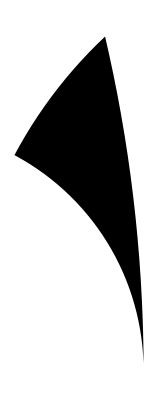

```mathematica
Graphics@rpdr[vanItersonRegion[{5,3},"Plus"]]
```

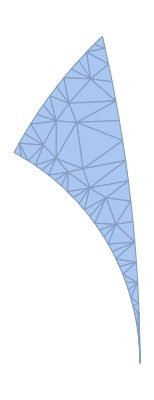

```mathematica
DiscretizeRegion[vanItersonRegion[{5,3},"Plus"],MaxCellMeasure->100,PrecisionGoal->6]
```

```mathematica
vanItersonTouchingCircle[{3,5}]
```

Circle[{7/16,0},1/16,{0,π}]

```mathematica
DiscretizeRegion[
 CSGRegion["Difference",
{
CSGRegion["Intersection",{vanItersonTouchingCSG[{2,3},0],vanItersonTouchingCSG[{3,5},0]}]
,
vanItersonTouchingCSG[{3,8},0.001]
}
]
]
```

```mathematica
vanItersonTouchingCircle[{3,8}]/.
```

Circle[{21/55,0},1/55,{0,π}]

```mathematica
CSGRegion["Intersection",{vanItersonTouchingCSG[{2,3},0],vanItersonTouchingCSG[{3,5},0]}]
```

-Graphics-

```mathematica
vanItersonPolygon[{5,3},"Plus"]
```

Polygon[…]

```mathematica
rpdr@vanItersonRegion[{5,3}, "PlusMinus"]
```

```mathematica
rpdr@vanItersonRegion[{5,3}, "Minus"]
```

Polygon[…]

```mathematica
Clear[vanItersonRegionBounds]
vanItersonRegionBounds[{0,1}] := {{-1/2,1/2},{0,1.2}};
vanItersonRegionBounds[{1,0}] := vanItersonRegionBounds[{0,1}] ;
vanItersonRegionBounds[{1,1}] := {{0,1/2},{0,1.2}} ;
vanItersonRegionBounds[{1,2}] := {{0,1/2},{0,1/3}};
vanItersonRegionBounds[mn_] := Module[{u,vn,vm,m,n},
{m,n}=Sort[mn];
 {u,vn}= euclideanWindingNumberPair[{m,n}];
 {u,vm}= euclideanWindingNumberPair[Reverse@{m,n}];
{tcCentre,tcRadius}= Take[List@@vanItersonTouchingCircle[{ n-m,n}],2];
{Sort[{vn/n,vm/m}],{0,tcRadius}}
]
```

```mathematica
gmnTheorem[w_] := (u  w- v)/(m   w-  n)
```

```mathematica
gmnSymbolic[w_] := (u  Subscript[Δ, nm] w+ v)/(m  Subscript[Δ, nm] w+ n)

Clear[m,n,u,v];
deltaSquaredOne = {Power[Subscript[Δ,nm],2]-> 1 ,Power[Subscript[Δ,nm],3]->Subscript[Δ, nm]};
gmnTheoremValues = <| "Zero"-> gmnTheorem[0],"Square"-> Together/@(ComplexExpand@ReIm[((ComplexExpand[gmnTheorem[I]] /. First@Solve[  n u - m v== Subscript[Δ, nm],v] //Expand) //.  deltaSquaredOne)])
,"Triple"-> Module[{},
tripleplt = (ComplexExpand@ReIm@ComplexExpand[gmnTheorem[1/2+ I Sqrt[3]/2]] //Simplify) /. First@Solve[  n u - m v== Subscript[Δ, nm],v] ;
res = Simplify[Map[Expand,(tripleplt  )]  //.  deltaSquaredOne];
Apart  /@ (res  //. deltaSquaredOne)
]
|>
gmnSymbolicValues = <| "Zero"-> gmnSymbolic[0],"Square"-> Together/@(ComplexExpand@ReIm[((ComplexExpand[gmnSymbolic[I]] /. First@Solve[  n u - m v== Subscript[Δ, nm],v] //Expand) //.  deltaSquaredOne)])
,"Triple"-> Module[{},
tripleplt = (ComplexExpand@ReIm@ComplexExpand[gmnSymbolic[1/2+ I Sqrt[3]/2]] //Simplify) /. First@Solve[  n u - m v== Subscript[Δ, nm],v] ;
res = Simplify[Map[Expand,(tripleplt  )]  //.  deltaSquaredOne];
Apart/@ (res )//. deltaSquaredOne
]
|>
```

<|Zero→v/n,Square→{(m^2 u+n^2 u-n Δ_nm)/(m (m^2+n^2)),-Δ_nm/(m^2+n^2)},Triple→{u/m+((m-2 n) Δ_nm)/(2 m (m^2-m n+n^2)),-(√3 Δ_nm)/(2 (m^2-m n+n^2))}|>

<|Zero→v/n,Square→{(m^2 u+n^2 u-n Δ_nm)/(m (m^2+n^2)),1/(m^2+n^2)},Triple→{(-1+m u)/m^2+(m^2+2 n^2)/(2 m^2 (m^2+n^2+m n Δ_nm)),(√3)/(2 (m^2+n^2+m n Δ_nm))}|>

```mathematica
regionToPolygon[r_] := Module[{rb,g,cblines,x,y,xy,c},
rb=RegionBoundary[r];
cblines = MeshCells[rb,1] /. Line[{x_,y_}] -> UndirectedEdge[x,y];
g = Graph[MeshCells[rb,0]/. Point[xy_]->xy,cblines,
VertexCoordinates->MeshPrimitives[rb,0]/. Point[xy_]->xy];
c = First@ConnectedGraphComponents[g];
Polygon[AnnotationValue[{c,FindHamiltonianPath[c]},VertexCoordinates]]
];
```

### Generating intervals

```mathematica
mnuvi[m_,n_,u_,v_] := Module[{dmaster,minterval,ninterval},
(* interval on which [md]=u and [nd]=v *)
dmaster = Interval[{0,1/2}];
minterval =  (u+Interval[ {-1/2,1/2}])/m;
ninterval =  (v+Interval[ {-1/2,1/2}])/n;
IntervalIntersection[dmaster,minterval,ninterval]
];
generatingInterval[{m_,n_}] :=  Module[{u,v,up,vp,resplus,resminus,res,dmaster},
dmaster = Interval[{0,1/2}];
{u,v }= euclideanWindingNumberPair[{m,n}];

resplus=mnuvi[m,n,u,v];
vp = n-v; up = m- u;
resminus =mnuvi[m,n,up,vp];
res = IntervalUnion[resminus,resplus];
res];
generatingOpposedInterval[{m_,n_}] := Module[{res,u,v},
{u,v}=euclideanWindingNumberPair[{m,n}];
res  = If[m==1, Interval[{1/(2n),1/n}],
Interval[{u/m,v/n}]
];
If[Min[res]≥ 1/2,res = 1-res];
res
];
```

## Principal Vectors

```mathematica
euclideanReduction[pq_]  := Module[{uv,it,firstShorter,dotPositive,reduceSecond,isPrincipal,positiveRise,positiveVec},
firstShorter[{u_,v_}] := Module[{u2=Simplify[u . u],v2=Simplify[v . v]},If [ u2 < v2, {u,v},{v,u}]];
	dotPositive[{u_,v_}] := If [ u . v > 0, {u,v},{u,-v}];
	reduceSecond[{u_,v_}] := If[ Abs[u . (v-u)]  >  Abs[u . v ],{u,v},{u,u-v}];	
	isPrincipal[{u_,v_}] := Module[{u2=Simplify[u . u],v2=Simplify[v . v]},
	u2  <=  v2 && 0  <= u . v && u . v <= u2 /2
	] ;
positiveRise[uvp_] := Map[positiveVec,uvp];
positiveVec[{ud_,uh_}] := If[uh>0,{ud,uh},
If[uh<0,{-ud,-uh}, (* h=0 *) {Abs[ud],0}]];
uv = pq;
it=1;While[!isPrincipal[uv], 
{
it++;  If[it>20,Break[]];
uv = firstShorter[uv];
uv = dotPositive[uv];
uv = reduceSecond[uv];
uv = Simplify /@uv ;
}];

uv = firstShorter[uv]; (* not needed but just to be clear *) 
uv = positiveRise[uv]; (* only do this at the end ! *)
uv
];
```

```mathematica
euclideanShortestPair[{pm_,pn_}] := 
(* in the lattice generated by pm and pn, what is the shortest pair ? *)
euclideanReduction[{pm,pn}];

tgetPrincipalVectorsDH[{d_,h_}] := Module[{uv},
uv= {{d,h}, {1-d,-h}}; (* (1,0) and (d,h) are a generating pair *)
euclideanShortestPair[uv]
];

vectorNorm2[x_] := Simplify[x . x]; 

tgetThreeParastichyVectorsDH[{d_,h_}] := Module[{pv,psum,pdiff,pthird,pvectors},
pv=tgetPrincipalVectorsDH[{d,h}];
psum = pv[[1]]+pv[[2]];
pdiff = pv[[1]]-pv[[2]]; If[pdiff[[2]] <0, pdiff = -pdiff];pthird = If[vectorNorm2[psum]<= vectorNorm2[pdiff],psum,pdiff];pvectors = Append[pv,pthird]; (* sometimes the fourth can be the same length as the third but we don't need to mark this *)
numberate[pvectors, h]
];
rawpnumber[v_,h_] :=  Module[{m,d},
If[v=={1,0},Return[0]];

m =Abs[Round[v⟦2⟧/h ]];
d = v⟦1⟧;
(* if d=-1/2, then there is another parastichy vector with d=1/2; if d not in [-1/2,1/2] also a complementary vector *)
If[d== -1/2 || Round[d] ≠ 0, m = hat[m]];
m
];
numberate[pvectors_, h_] := Module[{pnumbers,onepos,hatpos},pnumbers = Map[rawpnumber[#,h]&,pvectors];
onepos = Position[pnumbers,1,1];If[Length[onepos]>= 2, hatpos = onepos[[2]]; pnumbers[[hatpos]] = hat[1]];Association[Map[#[[1]]->#[[2]] &,Transpose[{pnumbers,pvectors}]]]
];
```

## Lattice geometry

```mathematica
latticeCreateDH[{d_,0}] := Nothing; (* silently drop from lists *) 

latticeCreateDH[{d_,h_},cylinderLU_:{-0.2,3.2},firstnEqual_:1]  :=  Module[{lattice},
lattice = Association [
"d"-> d
,"h"-> h
(* always has periodicity (1,0); this is how much of it we display: *) 
,"cylinder" -> { {-1/2,1/2},cylinderLU} 
(* the region of the unscaled, Euclidean cylinder we display  nodes from; normally the same, but not if we are applying a scaling to it *)
,"nodeCylinder" -> { {-1/2,1/2},cylinderLU} 
,"parastichyVectors" ->  tgetThreeParastichyVectorsDH[{d,h}]
,"scalings"-> <||>
];
lattice =Prepend[lattice,{ "parastichyNumbers"-> tgetParastichyNumbersGroupedByLength[lattice,firstnEqual]}];
lattice = Append[lattice,
{"namedLatticePoints"-> lNamedLatticePoints[lattice]}];
lattice
];
```

```mathematica
tgetParastichyNumbersGroupedByLength[lattice_,firstnEqual_] := Module[{pv,pvlengths,pva,i}, 
pv = latticeParastichyVectors[lattice];pvlengths =Map[vectorNorm2,pv];
pvlengths = SortBy[pvlengths,N];
(*  only if we make eg hexagonal lattices, the lengths may be algebraically but not numerically equal so we force them *)
For[i=2,i≤firstnEqual,i++,
pvlengths[[i]] = pvlengths[[1]]
];
pva = GroupBy[pvlengths,Identity,Sort[Keys[#]]&];Association[Map[ pva[#]-> # &, Keys[pva]]]
];

latticeParastichyNumbersGroupedByLength[lattice_] := Keys[lattice["parastichyNumbers"]];

latticeParastichyNumbers[lattice_] := Module[{pnumbers}, 
pnumbers =latticeParastichyNumbersGroupedByLength[lattice];Flatten[Map[Sort,pnumbers]]
];
```

```mathematica
(* at some point, rename lattice["cylinder"] to lattice["displayCylinder"] and rationalise *)
latticeGetCylinder[lattice_] := lattice["cylinder"];
latticeGetCylinderLU[lattice_] := lattice["cylinder"][[2]];
latticeGetNodeCylinder[lattice_] := lattice["nodeCylinder"];
latticeGetNodeCylinderLU[lattice_] := lattice["nodeCylinder"][[2]];

latticeSetDisplayCylinder[lattice_,cylinder_] := Module[{res},
res =lattice;
res["cylinder"] = cylinder;
res
];

latticeSetDisplayCylinderLU[lattice_,cylinderLU_] := Module[{res,cyl},
res =lattice;
cyl= lattice["cylinder"];
cyl[[2]] = cylinderLU;
res["cylinder"] = cyl;
res
];
(* resets both clyinder and nodeCylinder, might break otherwise *)
latticeSetCylinderLU[lattice_,cylinderLU_] := Module[{res},
res = lattice;
res =latticeSetDisplayCylinderLU[res,cylinderLU] ;
res =latticeSetNodeCylinderLU[res,cylinderLU] ;

res
];
latticeSetNodeCylinderLU[lattice_,cylinderLU_] := Module[{res,cyl},
res =lattice;
cyl= lattice["nodeCylinder"];
cyl[[2]] = cylinderLU;
res["nodeCylinder"] = cyl;
res = Append[res,
{"namedLatticePoints"-> lNamedLatticePoints[res]}];
res
];
```

```mathematica
latticeLabel[lattice_] := latticeParastichyNumbersGroupedByLength[lattice];
latticeLabelText[lattice_,upto_:2] := Module[{ll,tos},
ll =  latticeLabel[lattice] ;

tos[hat[n_]] := "\!\(\*OverscriptBox[\(" <> ToString[n] <> "\), \(^\)]\)";
tos[n_] := ToString[n];

(*tos[x_] := If[x===hat[1],"\!\(\*OverscriptBox[\(1\), \(^\)]\)",ToString[x]];*)
ll = Map[tos,ll,{2}];ll = Map[StringRiffle[#,"="]&,ll];ll = StringRiffle[Take[ll,UpTo[upto]],","]
];
```

```mathematica
latticeLabelPosition[lattice_] := Module[{cyl},
cyl=latticeGetCylinder[lattice];
{cyl[[1,1]],cyl[[2,2]]} (* top left *)
];

latticeParastichyVectors[lattice_] := lattice["parastichyVectors"];

latticePrincipalParastichyPair[lattice_] := Take[latticeParastichyNumbers[lattice],2];
latticePrincipal3ParastichyNumbers[lattice_] :=Take[latticeParastichyNumbers[lattice],3]
```

```mathematica
lNamedLatticePoints[lattice_] := Module[{nmin,nmax,irange,points,h,cylinderLU},h = lattice["h"];cylinderLU=lattice["nodeCylinder"][[2]];{nmin,nmax}= {Ceiling[Min[cylinderLU]/h],Floor[Max[cylinderLU]/h]};irange = {nmin,nmax};points = Association[ Table[i->N@First@latticePointWithCopies[lattice,i],{i,nmin,nmax}]];
points
]; 
(* will break any multijugacy *) 

lCalculateLatticePoints[lattice_] :=  Module[{nmin,nmax,irange,points,h,cylinderLU},h = lattice["h"];cylinderLU=lattice["nodeCylinder"][[2]];{nmin,nmax}= {Ceiling[Min[cylinderLU]/h],Floor[Max[cylinderLU]/h]};irange = {nmin,nmax};points = N@Flatten[Table[latticePointWithCopies[lattice,i],{i,nmin,nmax}],1];
points
];

latticePoints[lattice_] := Values[lattice["namedLatticePoints"] ];
latticeNamedPoints[lattice_]  := lattice["namedLatticePoints"];


latticePoints[lattice_,scalingFunction_] :=  Module[{},
(* if there is a scaling function, it takes the original set of points and maps them to {0,scaling[cylinderU] *)
Map[latticeScaling[lattice,scalingFunction],latticePoints[lattice]]
];
latticeNamedPoints[lattice_,scalingFunction_] :=  Module[{},
Map[latticeScaling[lattice,scalingFunction],latticeNamedPoints[lattice]]
];



latticeGraphicPoints[lattice_] :=  Point[latticePoints[lattice]];
latticeGraphicsPoint[lattice_,m_] :=  Point[latticePoint[lattice,m]];
```

```mathematica
mod[x_] :=  x - Round[x];

lpoint[{d_,h_},m_] := { mod [d m] , m h};
lpoint[{d_,h_},hat[m_]] := Module[{j,jp,jm},
j = lpoint[{d,h},m]; jp = j - {1,0}; jm = j+ {1,0}; (* should just test j[[1]]>0... *) 
If[ jp . jp < jm . jm, jp,jm]
];



latticePoint[lattice_,m_] :=lpoint[{lattice["d"],lattice["h"]},m];
latticePointWithCopies[lattice_,m_] := Module[{cylinder,lp,i,x},
(* including periodic copies within the display cylinder *) 
cylinder = latticeGetCylinder[lattice];
lp = latticePoint[lattice,m];
If[cylinder⟦1⟧== {-1/2,1/2},Return[{lp}]]; (* should be the same *)
x = lp⟦1⟧;
Return[Table[lp + i {1,0},{i,Ceiling[cylinder⟦1,1⟧-x],Floor[cylinder⟦1,2⟧-x]}]]
];

latticeVector[lattice_,m_] :=If[zeroParastichyQ[m],{1,0},latticePoint[lattice,m]];
```

```mathematica
latticePointH[lattice_,m_] := latticePoint[lattice,m][[2]];
latticePointD[lattice_,m_] := latticePoint[lattice,m][[1]];
latticeRise[lattice_] := lattice["h"] ;
latticeDivergence[lattice_] := latticePointD[lattice,1]; (* will be the same as lattice["d"] for -1/2<d<1/2 *) 
latticeVectorLength[lattice_,m_] :=  Norm[ latticeVector[lattice,m]];
```

### Graphics[] helper functions

```mathematica
latticeGraphicRegion[lattice_,scalingFunction_] := Module[{},
Switch[scalingFunction,
"Disk",glatticeDisk[lattice],
"Arena",glatticeScaledRegion[lattice,"Arena"],
"StemStretch",glatticeStemRegion[lattice],
"StemBulge",glatticeScaledRegion[lattice,"StemBulge"]
]
];


glatticeDisk[lattice_] := Module[{cylinderLU,func,innerOuter},
cylinderLU = latticeGetCylinderLU[lattice];
func[z_] := latticeScaling[lattice,"Disk"][{0,z}]⟦1⟧;
innerOuter = Map[func,Reverse[cylinderLU]];
innerOuter= Map[Ramp ,innerOuter];
innerOuter = Sort[innerOuter];
If[First@innerOuter==0,Disk[{0,0},Last[innerOuter]],Annulus[{0,0},innerOuter]]
];

glatticeScaledRegion[lattice_,scalingFunctionName_] := Module[{region,dregion,displayCylinder,cylinder,bfunc,x,z},
cylinder= latticeGetNodeCylinder[lattice];
bfunc = latticeScaling[lattice,scalingFunctionName];
region = Region@ParametricRegion[{bfunc[{x,z}],cylinder⟦1,1⟧<= x <= cylinder⟦1,2⟧ && cylinder⟦2,1⟧ <= z <= cylinder⟦2,2⟧},{x,z}];

displayCylinder = latticeGetCylinder[lattice];
dregion = DiscretizeRegion[region,displayCylinder]; (* mma bug sets region boundary wrongly *)
regionToPolygon@RegionBoundary[dregion]
];

glatticeStemRegion[lattice_] :=  Rectangle@@Transpose@latticeGetCylinder[lattice]
```

## Parastichy lines

```mathematica
latticePrincipal3ParastichyLines[lattice_] := Map[latticeParastichyLines[lattice,#]&,latticePrincipal3ParastichyNumbers[lattice]];

latticePrincipalParastichyLines[lattice_] := Map[latticeParastichyLines[lattice,#]&,latticePrincipalParastichyPair[lattice]];

barem[m_] :=m /. hat -> Identity;
zeroParastichyQ[m_] := barem[m] == 0;

latticeParastichySlope[lattice_,m_] := Module[{parastichyVectorM,pSlope},
parastichyVectorM = latticePoint[lattice,m];
 If[parastichyVectorM[[1]]==0 ,Return[∞]];
parastichyVectorM[[2]]/parastichyVectorM[[1]]
];

latticeParastichyVerticalSeparation[lattice_,m_] := Module[{parastichyVectorM,pSlope},
 If[zeroParastichyQ[m],Return[latticeRise[lattice]]];
parastichyVectorM = latticePoint[lattice,m];
 If[parastichyVectorM[[1]]==0 ,Return[0]];
pSlope = parastichyVectorM[[2]]/parastichyVectorM[[1]];
latticeRise[lattice]/pSlope
];

latticeParastichyHorizontalSeparation[lattice_,m_] := Module[{},
If[zeroParastichyQ[m],Return[1]];
1/barem[m]
];
```

```mathematica
linelineIntersection[line1_,line2_] := Module[{x1,y1,x2,y2,x3,y3,x4,y4,x,y,m1,m2},
{ {x1,y1},{x2,y2} } = line1;
{{ x3,y3},{x4,y4}} = line2;
m1 = { {x,y,1},{x1,y1,1},{x2,y2,1}};
m2 = {{ x,y,1},{x3,y3,1},{x4,y4,1}};
{x,y}  /. Solve[{Det[m1]==0,Det[m2]==0},{x,y}][[1]]
];
```

```mathematica
latticeParastichyCylinderIntersection[lattice_,m_,topbottom_] :=Module[{arena,arenaBottomIntersection,arenaTopIntersection},
If[zeroParastichyQ[m],Abort[]];
arena = latticeGetNodeCylinder[lattice];
arenaBottomIntersection = linelineIntersection[{{  arena[[1,1]], arena[[2,1]]},{ arena[[1,2]],arena[[2,1]]}},{ {0,0},  latticeVector[lattice,m]}][[1]];arenaTopIntersection = linelineIntersection[{{  arena[[1,1]], arena[[2,2]]},{ arena[[1,2]],arena[[2,2]]}},{ {0,0},  latticeVector[lattice,m]}][[1]];If[topbottom===Bottom,arenaBottomIntersection,arenaTopIntersection]
];
```

```mathematica
(* this is a set of xz points on the euclidean cylinder through which m distinct m-parastichies will go *)
latticeParastichyXZThrough[lattice_,m_] :=  Module[{arena,ilowerB, iupperB,translationD,arenaBottomIntersection},
arena = latticeGetNodeCylinder[lattice];
If[zeroParastichyQ[m],
translationD = latticeParastichyVerticalSeparation[lattice,0];ilowerB = -Floor[(  - arena⟦2,1⟧)/translationD];iupperB = Floor[(arena⟦2,2⟧)/ translationD];
Return[Table[{arena⟦1,1⟧,i *  translationD},{i,ilowerB,iupperB}]]
];
(* or a slope *)
translationD= Abs[latticeParastichyHorizontalSeparation[lattice,m]];

arenaBottomIntersection = linelineIntersection[{{  arena⟦1,1⟧, arena⟦2,1⟧},{ arena⟦1,2⟧,arena⟦2,1⟧}},{ {0,0},  latticeVector[lattice,m]}]⟦1⟧;ilowerB = -Floor[( arenaBottomIntersection - arena⟦1,1⟧)/translationD];iupperB = Floor[(arena⟦1,2⟧- arenaBottomIntersection )/ translationD];Return[Table[{arenaBottomIntersection+ i *  translationD,arena⟦2,1⟧},{i,ilowerB,iupperB}]]

];
```

```mathematica
latticeParastichyLines[lattice_,m_] :=  Module[{xtable },
xtable= latticeParastichyXZThrough[lattice,m];
 Map[latticeParastichyLinesThroughXZ[lattice,m,#]&,xtable]
];
latticeParastichyLines[lattice_,m_,k_] := latticeParastichyLinesThroughXZ[lattice,m,latticePoint[lattice,k]];
latticeParastichyLinesAbove[lattice_,m_,k_] := latticeParastichyLinesAboveXZ[lattice,m,latticePoint[lattice,k]];
```

```mathematica
latticeParastichyLinesAboveXZ[lattice_,m_,throughxz_] := Module[{res,cylinderLU,lines},
cylinderLU = latticeGetNodeCylinderLU[lattice];
cylinderLU[[1]] = throughxz [[2]];
res = latticeSetNodeCylinderLU[lattice,cylinderLU];
lines = latticeParastichyLinesThroughXZ[res,m,throughxz];
lines
];


latticeParastichyLinesThroughXZ[lattice_,m_,throughxz_] := Module[{pvecslope,bottom,top,cylinder,cylinderLU,line},
cylinder = latticeGetNodeCylinder[lattice];cylinderLU = cylinder⟦2⟧;If[zeroParastichyQ[m], (* parastichy is horizontal *)
line = {{cylinder⟦1,1⟧,throughxz⟦2⟧},{cylinder⟦1,2⟧,throughxz⟦2⟧}},
(* or *) 
If[latticePoint[lattice,m][[1]]==0, (* parastichy is vertical *) 
line ={ {throughxz⟦1⟧,cylinder⟦2,1⟧},{throughxz⟦1⟧,cylinder⟦2,2⟧}},
(* or general case *) 
pvecslope = latticeParastichySlope[lattice,m];bottom = { (cylinderLU⟦1⟧-throughxz⟦2⟧)/pvecslope +throughxz⟦1⟧, cylinderLU⟦1⟧};top        = { (cylinderLU⟦2⟧-throughxz⟦2⟧)/pvecslope+throughxz⟦1⟧,cylinderLU⟦2⟧};
line = splitLineOverCylinder[cylinder,bottom,pvecslope];
]
];

Line[line]
];

splitLineOverCylinder[cylinder_,bottom_,pvecslope_] := Module[{line,lastXZ,i,nextX,nextZ},
line = {};
lastXZ = bottom;
i=0;
While[
nextX = If[pvecslope>0, cylinder⟦1,2⟧,cylinder⟦1,1⟧ ];
nextZ = lastXZ⟦2⟧+(nextX-lastXZ⟦1⟧)* pvecslope; (* assumes cylinder width a multiple of 1 *)
If[nextZ> cylinder⟦2,2⟧,
nextZ =  cylinder⟦2,2⟧;
nextX = lastXZ⟦1⟧+(nextZ-lastXZ⟦2⟧)/pvecslope
];
line = Append[line,{lastXZ,{nextX,nextZ}}];
i++;
i< 50 && nextZ  < cylinder⟦2,2⟧,
(* While body *)
lastXZ = Last@Last[line];
lastXZ⟦1⟧ = If[pvecslope>0, cylinder⟦1,1⟧,cylinder⟦1,2⟧ ]
];
line
];
```

```mathematica
latticeParallelogram[lattice_,m_,n_,through_] :=Module[{origin,pm,pn},
origin = latticePoint[lattice,through]; pm=latticePoint[lattice,m];pn=latticePoint[lattice,n];
 { origin, origin+pm,origin+pm+pn,origin+pn,origin}
];
```

```mathematica
latticeGraphicsCylinder[lattice_] :=  Rectangle @@ Transpose[latticeGetCylinder[lattice]];
latticeGraphicsPlotRange[lattice_] :=  latticeGetCylinder[lattice];
```

## Drawing van Iterson space

## Renormalisations

```mathematica
latticeRenormalised[lattice_] := Module[{tran,zn,w1,pm,pn},
(* rotate and scale so that the old m-th parastichy vector is now (1,0) *){pm,pn} = latticePrincipalParastichyPair[lattice];tran = latticeRenormalisationTransformation[lattice,pm] ;(* that maps m to 0. we need a linearly independent n *)zn = latticePoint[lattice,pn];w1 = tran [ zn]; 
 (* should already have -1/2<d<1/2; role of this is to change w_-1 to w1 *)  
w1 = dhPrincipalPoint[w1];
latticeCreateDH[w1]
];

dhPrincipalPoint[{d_,h_}] := Module[{principaldh},
	principaldh = {mod[d],h};
If[h>0,principaldh,-principaldh]
];

latticeRenormalisationTransformation[lattice_,mvec_] := Module[{mEnd,mVectorLength,rot,sca,tran},
mEnd = latticePoint[lattice,mvec];mVectorLength = latticeVectorLength[lattice,mvec];rot = RotationTransform[{mEnd,{1,0}}];sca = ScalingTransform[{1/mVectorLength,1/mVectorLength}];tran = Composition[sca,rot];tran
];
```

## Lattices by transformation

### Mobius function definitions

```mathematica
(* relative to (0,1 ) not used *) 
(*hMN[{m_,n_}][w_]:= Module[{u,v},{u,v}= windingNumberPair[{m,n}];hMNUV[m,n,u,v,w]];
hMNRealPair[{m_,n_}] := Function[{xy},Module[{x,y},{x,y}=xy; ReIm[hMN[{m,n}][x +  I y]]]];
hMNRealPairReflection[{m_,n_}] := Function[{xy},Module[{x,y},
{x,y} = hMNRealPair[{m,n}][xy];
{1-x,y}
]];
hMNInDHalf[{m_,n_}] := If[euclideanDelta[{m,n}]==1,hMNRealPair[{m,n}],hMNRealPairReflection[{m,n}]];

hMNUV[m_,n_,u_,v_,w_]:=(-u w + v)/(-m w + n);
hMNUV[m_,n_,u_,v_,DirectedInfinity[_]]:=u/m;*)
```

```mathematica
(* relative to (1,0)  *) 


gMN[{m_,n_}][w_]:= Module[{u,v},{u,v}= euclideanWindingNumberPair[{m,n}];gMNUV[m,n,u,v,w]];
gMNRealPair[{m_,n_}] := Function[{xy},Module[{x,y},{x,y}=xy; ReIm[gMN[{m,n}][x +  I y]]]];
gMNRealPairReflection[{m_,n_}] := Function[{xy},Module[{x,y},
{x,y} = gMNRealPair[{m,n}][xy];
{1-x,y}
]];
gMNInDHalf[{m_,n_}] :=Function[{xy},
Module[{x,y},
{x,y} = N@gMNRealPair[{m,n}][xy];
x = x-Round[x];
If[x<0,x=-x];
{x,Abs[y]}
]];
(*gMNInDHalfExact*)
gMNInDHalfSymbolic[{m_,n_}] :=Function[{xy},
Module[{x,y},
{x,y} = gMNRealPair[{m,n}][xy];
x = x-Round[x];
If[x<0,x=-x];
{x,y}
]];
(*gMNInDHalf[{m_,n_}]  := 
 If[euclideanDelta[{m,n}]==1,gMNRealPair[{m,n}],gMNRealPairReflection[{m,n}]];
*)
gMNUV[m_,n_,u_,v_,w_]:=(v w + u)/(n w + m);
gMNUV[m_,n_,u_,v_,DirectedInfinity[_]]:=v/n;
```

```mathematica
viiMoebiusTransform[{{m_,n_},{u_,v_}}][{d_,h_}] := 
{(d^2 m u+h^2 m u+n v-d (n u+m v))/(d^2 m^2+h^2 m^2-2 d m n+n^2),h/(d^2 m^2+h^2 m^2-2 d m n+n^2)}
```

```mathematica
Module[{mvnu1,z1d,z1h},
Block[{d,h,m,v,n,u},
mvnu1 = Solve[ m v - n u ==1, v][[1]];
{z1d,z1h} = 
 Simplify/@( ComplexExpand@ ReIm [gMNUV[m,n,u,v,d+ I h]] );{z1d,z1h} - viiMoebiusTransform[{{m,n},{u,v}}][{d,h}] /. mvnu1]
]
```

{-(d^2 m u+h^2 m u+(n (1+n u))/m-d (1+2 n u))/(d^2 m^2+h^2 m^2-2 d m n+n^2)+(m (u+(d (1+n u))/m)+n (d u+(d^2 (1+n u))/m+(h^2 (1+n u))/m))/(m^2+2 d m n+(d^2+h^2) n^2),-h/(d^2 m^2+h^2 m^2-2 d m n+n^2)+h/(m^2+2 d m n+(d^2+h^2) n^2)}

```mathematica
latticeMoebiusTransform[mn_][dh_] := gMNInDHalf[mn][dh];


latticeMoebiusTransform[{1,0}][{0,0}] := {1/2,∞};
latticeMoebiusTransform[{1,0}][{0.,0.}] := {1/2,∞};
latticeMoebiusTransform[{0,1}][{d_,h_}]  := {d,h};
```

### Find special lattices

```mathematica
latticeHexagonal [{m_,n_},cylinderLU_:{-0.2,3.2}] := 
latticeCreateDH[latticeDHHexagonal[{m,n}],cylinderLU,3];
```

```mathematica
latticeDHNonOpposedTC[{m_,n_}]  := Module[{xy,r,angles,circle},
(*circle =  viiPrimaryNonOpposed[{m,n}];
*)circle =  vanItersonTouchingCirclePrimaryNonOpposed[{m,n}];
If[circle==Nothing,Return[Nothing]];
{xy,r,angles} = List @@ circle;
angles = Mean[angles];
xy + r * {Cos[angles],Sin[angles]}
]


latticeTriplePoint[{m_,n_}] := latticeDHHexagonal[{m,n}];latticeDHHexagonal[{m_,n_}]  := latticeMoebiusTransform[{m,n}][ { 1/2,Sqrt[3]/2}];


latticeTouchingCircle[{m_,n_},cylinderLU_:{-0.2,3.2}] := latticeCreateDH[
latticeMoebiusTransform[{m,n}][ {Cos[5π/12],Sin[5π/12]}],cylinderLU,2];
latticeEquiLength[{m_,n_},cylinderLU_:{-0.2,3.2}] := (* ie p numbers are (m+n),m=n *)latticeCreateDH[latticeMoebiusTransform[{m,n}][ {Cos[π/6],Sin[π/6]}],cylinderLU];
latticeOrthogonal[{m_,n_},cylinderLU_:{-0.2,3.2}] := latticeCreateDH[latticeMoebiusTransform[{m,n}][ { 0,1}],cylinderLU,2];
latticeWithMN[{m_,n_},cylinderLU_:{-0.2,3.2}] := latticeCreateDH[
latticeMoebiusTransform[{m,n}][{0.1,(Sqrt[3]/(2)-.25)}],cylinderLU];
```

```mathematica
latticeCircles[lattice_] := Module[{latticeMargin,lplus,lminus,r,cylinderLU,latticep},cylinderLU = latticeGetNodeCylinder[lattice][[2]];cylinderLU = cylinderLU + {-latticeRise[lattice],latticeRise[lattice]};latticeMargin = latticeSetCylinderLU[lattice,cylinderLU];latticep =  latticePoints[latticeMargin] ;lplus = latticep+ Table[{1,0},Length[latticep]];lminus =  latticep + Table[{-1,0},Length[latticep]];r =latticeDiskRadius[latticeMargin];Map[Circle[#,r]&,Join[ latticep,lplus,lminus]]
];

latticeDiskRadius[lattice_] := Module[{pv1},
	pv1 = latticeParastichyVectors[lattice][First[latticePrincipalParastichyPair[lattice]]];
	Norm[pv1 ]/2
];
```

## van Iterson regions

```mathematica
(*viiPrimaryOpposed[mn_]  := getCircleBranch[mn,"Opposed"];
viiPrimaryNonOpposed[mn_]  := getCircleBranch[mn,"NonOpposed"];
*)
(*getCircleBranch[{m_,n_},scalingFunction_] := Module[{mn,angle,upperpt,lowerpt,res,centre,r,theta12,branch},
mn = Sort[{m,n}];
branch = vanItersonTouchingCirclePrimary[mn];
If[!viiPrimaryIsEverNonOpposed[mn],
	If[scalingFunction=="Opposed", Return[branch],Return[Nothing[]]]];
angle = circleAngleAtLine[branch,viiOrthostichyD[mn]];
upperpt = viiTriplePoint[viiUpperPair[mn]];
lowerpt = viiTriplePoint[mn];

{centre,r,theta12} = Apply[List,branch];
If[scalingFunction=="NonOpposed",
res = Circle[centre,r,Sort@{xyToArg[branch,upperpt],angle}]
,
res = Circle[centre,r,Sort@{xyToArg[branch,lowerpt],angle}]
];
Return[res];
];*)
```

```mathematica
(*viiMNSemiCircle[mn_] := Module[{r,m,n,u,v,dbar},
{m,n}= Sort[mn];
If[m==1 && n==1,Return[InfiniteLine[{{1/2,0},{1/2,1}}]]];
r = 1/(n^2-m^2);
{u,v} = euclideanWindingNumberPair[{m,n}]; 
dbar = ( n v - m u )/(n^2-m^2);
Circle[ { dbar, 0},r,{0,π}]
];*)
(*
viiUpperPair[{m_,n_}] := {Abs[n-m],Min[m,n]}
*)
(*
viiPrimarySegment[mn_] :=  Module[{upperTP,lowerTP,m,n},
{lowerTP,upperTP} = vanItersonTouchingCirclePrimaryBoundingBox[mn];
subSegment[viiMNSemiCircle[mn],upperTP,lowerTP]
];
viiPrimarySegment[{1,1}] = Line[{{1/2,(√3)/2},{1/2,1/(2 √3)}}];
viiPrimarySegment[{0,1}] = Circle[{0,0},1,{π/3,π/2}];
*)






viiMNOrthoCircle[mn_] := Module[{m,n,u,v,um,vn},
{m,n}= mn;
{u,v} = euclideanWindingNumberPair[mn];
{um,vn} = {u/m,v/n};
Circle[ { (um+vn)/2, 0},Abs[vn-um]/2,{0,π}]
];

dr[r_] := DiscretizeRegion[r];
Clear[viiRegion]

viiRegion[{0,1},"Ordered","Plus",hmax_:20]  := RegionDifference[
Rectangle[{0,0},{1/2,hmax}],Disk[{0,0},1,{0,π}]];
viiRegion[{0,1},"Ordered","Minus",hmax_:20] :=RegionDifference[
Rectangle[{-1/2,0},{0,hmax}],Disk[{0,0},1,{0,π}]];
viiRegion[{0,1},"Ordered"] :=RegionUnion[viiRegion[{0,1},"Ordered","Plus"],viiRegion[{0,1},"Ordered","Minus"]];

viiRegion[{1,0},"Ordered","Plus"]  := RegionDifference[
RegionIntersection[Rectangle[{0,0},{1,1}],Disk[{0,0},1,{0,π}]],
Disk[{1,0},1,{0,π}]
];
viiRegion[{1,0},"Ordered","Minus"] := RegionDifference[
RegionIntersection[Rectangle[{-1,0},{0,1}],Disk[{0,0},1,{0,π}]],
Disk[{-1,0},1,{0,π}]
];

viiRegion[{1,0},"Ordered"] :=RegionUnion[viiRegion[{1,0},"Ordered","Plus"],viiRegion[{1,0},"Ordered","Minus"]];

viiRegion[{0,1},"All"] := RegionUnion[viiRegion[{0,1},"Ordered"],viiRegion[Reverse@{0,1},"Ordered"]];
viiRegion[{1,0},"All"] = viiRegion[{0,1},"All"];viiRegion[{1,1},"All"] := viiRegion[{1,1},"Ordered"];
viiRegion[{1,0}] := viiRegion[{1,0},"Ordered"]

viiRegion[mn_,"All"] := RegionUnion[viiRegion[mn,"Ordered"],viiRegion[Reverse@mn,"Ordered"]];

(* 1,1 *) 
If["Fix bug with region order",
(
viiRegion[{1,1},"Ordered","Minus"]  :=   
RegionIntersection[ Rectangle[{0,0},{1/2,1}]
,RegionDifference[Disk[{1,0},1,{0,π}],
viiMNOrthoCircle[{1,1}] /. Circle-> Disk
]
];

viiRegion[{1,1},"Ordered","Plus"]  :=   
RegionIntersection[ Rectangle[{0,0},{1/2,1}]
,RegionDifference[
viiMNOrthoCircle[{1,1}] /. Circle-> Disk
,Disk[{1/3,0},1/3,{0,π}]
]
];
viiRegion[{1,1},"Ordered"] :=RegionUnion[viiRegion[{1,1},"Ordered","Plus"],viiRegion[{1,1},"Ordered","Minus"]];


viiRegion[{2,1},"Ordered"] := Module[{m,n,outer,inner1,inner2},
outer = Rectangle[{0,0},{1/2,1}];
inner1 = Disk[{2/3,0},1/3,{0,π}];
inner2 = viiMNSemiCircle[{1,3}]/. Circle->Disk;
RegionDifference[ RegionIntersection[outer,inner1],inner2]
];
viiRegion[{1,2},"Ordered"] := Module[{m,n,outer,inner1,inner2},
outer = Disk[{1/3,0},1/3,{0,π}];
inner1 =Disk[{2/3,0},1/3,{0,π}];
inner2 = viiMNSemiCircle[{2,3}]/. Circle->Disk;
RegionDifference[outer,RegionUnion[inner1,inner2]]
];

(* this is the bit that will probably work if i concentrate. but it doesn't *)
viiRegion[mn_,"All"] := Module[{m,n,outer,inner,outer1,outer2,inner1,inner2},
{m,n}= Sort[mn];
outer1 = viiMNSemiCircle[{Abs[n-m],m}]/. Circle->Disk;outer2 = viiMNSemiCircle[{Abs[n-m],n}]/. Circle->Disk;
If[euclideanDelta[{m,n}]==1,
outer = RegionDifference[outer2,outer1],
outer = RegionIntersection[outer1,outer2]
];
inner1 = viiMNSemiCircle[{m,n+m}]/. Circle->Disk;
inner2 = viiMNSemiCircle[{n,n+m}]/. Circle->Disk;
inner = RegionUnion[inner1,inner2];
RegionDifference[outer,inner]
];

viiRegion[mn_,"Ordered"] := Module[{m,n,outer,inner},
{m,n}=mn;
outer = viiRegion[mn,"All"];
inner = viiMNSemiCircle[{m,n}]/. Circle->Disk;
If[m<n,
RegionDifference[outer,inner]
,
RegionIntersection[outer,inner]
]
];

viiRegion[mn_,"Ordered",sign_] := Module[{m,n,outer,inner},
outer =  viiRegion[mn,"Ordered"];inner = viiMNOrthoCircle[mn]/. Circle->Disk;
If[sign=="Minus",
RegionDifference[outer,inner]
,
RegionIntersection[outer,inner]
]
]
)(* end of code unused cos of bug *)];
Clear[tRegionBase];
tRegionBase["Ordered", sign_] :=  tRegionBase["Ordered", sign] = regionToPolygon[DiscretizeRegion[viiRegion[{1,0},"Ordered",sign]]];
tRegionBase["Ordered"] :=  tRegionBase["Ordered"] = regionToPolygon[DiscretizeRegion[viiRegion[{1,0},"Ordered"]]];
tRegionBase["All"] :=  tRegionBase["All"] = regionToPolygon[
DiscretizeRegion[viiRegion[{1,0},"All"]]];

transformPolygon[poly_,function_] := Polygon[ function  /@ (First@Apply[List,poly])];

(* special case *) 
viiPolygon[{0,1},args__] :=  regionToPolygon[DiscretizeRegion[viiRegion[{0,1},args]]];
(* base case *)
viiPolygon[{1,0},args__] :=  tRegionBase[args]
(* transform case *)
viiPolygon[mn_,args__] :=  transformPolygon[tRegionBase[args],gMNInDHalf[mn]]
viiPolygon[mn_] := viiPolygon[mn,"All"]




viiTriplePoint[mn_] := gMNInDHalf[mn][{1/2,Sqrt[3]/2}];
viiTriplePoint[{0,1}] := {-1/2,Sqrt[3]/2}; (* algo gives (3/2,Sqrt[3]/2) *)

viiLabelPoint[mn_] := gMNInDHalf[mn][{0,Sqrt[3]/(5/2)}];
viiTouchingCircleLabel[mn_] :=  gMNInDHalf[mn][{0,1}];
viiTouchingCircleLabelNonPrimary[mn_] :=  gMNInDHalf[mn][{-Sqrt[3]/2,1/2}];
```

```mathematica
viiTouchingCircleLabelNonPrimary[{1,2}] = gMNInDHalf[{1,2}][{Sqrt[3]/2,1/2}];
```

### Get Region and Transform to work together

```mathematica
(* https://mathematica.stackexchange.com/questions/11430/why-doesnt-normal-work-on-geometrictransformation *)
(* at one point this was needed - may not be at present *) 

NormalizeGraphics[g_]:=Internal`InheritedBlock[{System`Private`InternalNormal},Unprotect[System`Private`InternalNormal];
System`Private`InternalNormal[gr:_Rotate|_Translate|_Scale|_GeometricTransformation,_]:=Module[{tmp=Quiet[transform2D[gr],TransformedRegion::reg]},tmp/;Head[tmp]=!=TransformedRegion];
Normal[g,{Rotate,Scale,Translate,GeometricTransformation}]]

transform2D[Rotate[g_,r_,p___]]:=TransformedRegion[g,RotationTransform[r,absolutePosition[g,p]]]

transform2D[Translate[g_,t_]]:=TransformedRegion[g,TranslationTransform[t]]

transform2D[Scale[g_,s_,p___]]:=TransformedRegion[g,ScalingTransform[s,absolutePosition[g,p]]]

transform2D[GeometricTransformation[g_,tf_]]:=TransformedRegion[g,tf/.Except[_TransformationRegion]:>AffineTransform[tf]]

absolutePosition[g_]:=absolutePosition[g,{Center,Center}]
absolutePosition[g_,{h:(Left|Center|Right),v:(Top|Center|Bottom)}]:=Module[{hrange,vrange},{hrange,vrange}=RegionBounds[g][[;;2]];
{Replace[h,{Left->Min,Center->Mean,Right->Max}][hrange],Replace[v,{Bottom->Min,Center->Mean,Top->Max}][vrange]}]
absolutePosition[g_,spec_]:=spec
```

## Noneuclidean lattices

scalingFunction is the name of a z - stretch function stored in the lattice
For Disk this will be used to map the cylinder onto a disk
For StemStretch onto a z-stretched cylinder
For Arena a general x-z map

```mathematica
latticeSetScaling[lattice_,funcNameValue_] := 
Module[{res},
res = lattice;
res["scalings"] = AppendTo[res["scalings"],funcNameValue];
res
];
latticeScaling[lattice_,scalingFunction_] := Module[{res},
res = lattice["scalings"][scalingFunction];
If[MissingQ[res],Print["No ", scalingFunction , " scaling set"]];
res
];

latticeParastichyFunctions[lattice_,m_,k_,scalingFunction_] := Module[{cylinderLU,xInner,xOuter,data,xzfunc,scalefunc,funcs,interp,segments},
scalefunc = latticeScaling[lattice,scalingFunction];
If[scalingFunction=="Disk", (* mapping to periodic coordinates *)
cylinderLU= latticeGetNodeCylinderLU[lattice];
xOuter = latticeParastichyCylinderIntersection[lattice,m,Bottom]+ k * latticeParastichyHorizontalSeparation[lattice,m];
xInner = xOuter + (cylinderLU⟦2⟧-cylinderLU⟦1⟧)/latticeParastichySlope[lattice,m];
data = { { {0}, {xOuter,cylinderLU⟦1⟧}},{{1},{xInner,cylinderLU⟦2⟧}}};
xzfunc = Interpolation[data,InterpolationOrder->1];
funcs = {Function[{t},scalefunc[xzfunc[t]]]};
, (* for "Arena", "StemStretch", need the image of the parastichy line in the cylinder *) 
(*segments =First[List@@latticeParastichyLinesAbove[lattice,m,k]];*)
segments =First[List@@latticeParastichyLines[lattice,m,k]];
interp[seg_]:= Function[t,seg⟦1⟧(1-t)+ seg⟦2⟧ t ];
funcs = Map[Function[t,scalefunc[interp[#][t]]]&,segments];
];

funcs
];
```

## Stem shape functions

Probably need to be rewritten but used by Goethe

u, goes from 0 to 1 as angular parameter, 
v goes from 0 to 1 while s goes from 0 to smax while z goes over cylinderLU
s is the arc length measured along the boudary of the bulge=arc length in vertical direction on surface
map between s and v (hence z) is nonlinear for curved radius=circumference /2π  functions
a rise of 1 in base (x,z) lattice is an increase of s by 1 in (u,s) lattice

```mathematica
Clear[stemAddShape];stemAddShape[lattice_,circumferenceFunction_,unrolling_:1] := Module[{stem,surfaceFunctionUV,displayCylinder,vFunctionArcLength,xyScaling,radius,rmax},
stem =  Append[lattice,{"circumferenceFunctionV"->circumferenceFunction}];
vFunctionArcLength = tcalcStemVofS[stem]; (* hide gory details behinf local var name *)
stem = Append[stem,{"vArcLengthInverseS"-> vFunctionArcLength}];stem = Append[stem,{"arcLengthSRange"-> N@{0,stemSOfV[stem][1]}}];

surfaceFunctionUV = stemMakeSurfaceFunctionUV[stem,unrolling];
stem = Append[stem, {"surfaceXYZofUV"-> surfaceFunctionUV}];
displayCylinder = latticeGetCylinder[stem];
rmax =tFindMaxRadius[stem];

displayCylinder = {{-rmax,rmax}, MinMax@{surfaceFunctionUV[0,0][[3]],surfaceFunctionUV[0,1][[3]]}};stem = latticeSetDisplayCylinder[stem,displayCylinder];

stem
];

stemShapeFunctionUV[stem_] := stem["surfaceXYZofUV"]; 
stemRadiusFunctionV[stem_] :=Function[v,stem["circumferenceFunctionV"][v]/(2π)];
stemVofS[stem_] := stem["vArcLengthInverseS"]; 

stemSetDisplayRadius[stem_,radius_] := Module[{displayCylinder},
displayCylinder = latticeGetCylinder[stem];
displayCylinder[[1]] = 1.05* {-radius,radius};
latticeSetDisplayCylinder[stem,displayCylinder]
];

tFindMaxRadius[stem_] := Module[{radius,rmax}, (* often fails... *)
radius[v_?NumericQ] := stemRadiusFunctionV[stem][v];
Off[NIntegrate::inumr,Interpolation::indat];
rmax =1.05 * FindMaximum[{radius[v],0< v<1},{v,1/2}][[1]];
On[NIntegrate::inumr,Interpolation::indat];
rmax
];
```

```mathematica
(* true but not needed
stemRadiusFunctionS[stem_] :=Function[s,stemRadiusFunctionV[stem][stem["vArcLengthInverseS"][s]]];
*)
(* work in arc length parameter s *)
stemSOfV[stem_] := Module[{func=stemRadiusFunctionV[stem]}, Function[{v},
Block[{s},N@ArcLength[func[s],{s,0,v}]]]];
(* invert *) 
tcalcStemVofS[stem_] := Module[{sofVTable},
      (* maps (0,smax ) to (0,1)  *) 
sofVTable = Table[{stemSOfV[stem][v],v},{v,0,1,0.01}];Interpolation[sofVTable] (* store instance stem<||> so we don't recalculate *) 
];

stemMakeSurfaceFunctionUV[stem_,unrolling_] := Module[{cylinderLU,surfaceCylinderLU,r,smax,func},
smax = stem["arcLengthSRange"][[2]];
cylinderLU =latticeGetNodeCylinderLU[stem];
surfaceCylinderLU = {0, (cylinderLU[[2]]-cylinderLU[[1]])/smax};
r = stemRadiusFunctionV[stem];
(* a radius function of 1 will correspond to a cylinder with circumference  2 pi  .. *) 
(* we allow it to be a rolled cylinder *)
unroll[s_] := Module[{offset},
offset = π s +π/2;
Function[{u,v},Append[r[v]*({0,1/s}+1/s * { Cos[ 2 π  s u   -offset ],  Sin[ 2 π s u -offset]}), tHeightFunctionCylinder[surfaceCylinderLU,v]]
]
];
unroll[0] = Function[{u,v},2*π * r[v]*{(u-1/2),0}];
func  = If[unrolling==1,
Function[{u,v}, {r[v] * Cos[ 2 π u], r[v] * Sin[ 2 π u], tHeightFunctionCylinder[surfaceCylinderLU,v]} ]
,
unroll[unrolling]
];
func
];
tHeightFunctionCylinder[cylinderLU_,v_] := cylinderLU[[1]] + v (cylinderLU[[2]] -cylinderLU[[1]]);
tSFunctionCylinder[cylinderLU_,h_] := (h-cylinderLU[[1]])/(cylinderLU[[2]] -cylinderLU[[1]])

(*
stemSurfaceFunctionUS[stem_] := Module[{surfaceFunction,sFunction},
surfaceFunction = stem["surfaceXYZofUV"];
sFunction = stem["vArcLengthInverseS"];
Function[{u,s},surfaceFunction[u,sFunction[s]]]
];






stemShapeFunctionUS[stem_] := Function[{u,s},
stemShapeFunctionUV[stem][u,stem["vArcLengthInverseS"][s]]
];

stemShapeLU[lattice_] := MinMax@{stemShapeFunctionUV[lattice][0,0][[3]],stemShapeFunctionUV[lattice][0,1][[3]]};


*)
```

```mathematica
(*stemParastichyOfV[stem_,m_,n_][v_] := Module[{dL,pslope,h,vscale,shapeLU},
dL = latticeParastichyCylinderIntersection[stem,m,Bottom]+n*latticeParastichyHorizontalSeparation[stem,m];pslope = latticeParastichySlope[stem,m];shapeLU =stemShapeLU[stem];vscale = shapeLU[[2]]-shapeLU[[1]]; (* h ranges over this as v goes from 0 to 1 *) 
h =  v * vscale ; 
stemPositionDH[stem,{ dL +h /pslope,h}] 
];
*)
stemParastichyOfV[stem_,m_,n_][v_] := Module[{s},
s =  stemSOfV[stem][v]; 
stemParastichyOfS[stem,m,n][s] 
];

stemParastichyOfS[stem_,m_,n_][s_] := Module[{dL,pslope,h,baseCylinderLU,smax,u,v},
dL = latticeParastichyCylinderIntersection[stem,m,Bottom]+n*latticeParastichyHorizontalSeparation[stem,m];pslope = latticeParastichySlope[stem,m];

baseCylinderLU = latticeGetNodeCylinderLU[stem];
smax = stem["arcLengthSRange"][[2]];
h =  s/smax *  (baseCylinderLU ⟦2⟧- baseCylinderLU ⟦1⟧); 
u =  dL +h /pslope;
u  = u - Round[u]+1/2 ;
v = stemVofS[stem][s];
stemShapeFunctionUV[stem][ u,v]
];

stemDHToUV[stem_] := Function[{dh},Module[{d,h,u,s,v,cylinderLU},d=dh⟦1⟧;h=dh⟦2⟧;
u = d - Round[d]+1/2;
cylinderLU =latticeGetNodeCylinderLU[stem];
smax =  stem["arcLengthSRange"][[2]];
s = smax*tSFunctionCylinder[cylinderLU,h];
v = stemVofS[stem][s];
{u,v}
]];

stemPoints[stem_] := Module[{basePoints,uvPoints,uvToXYZ},
basePoints = latticeNamedPoints[stem];
uvPoints = Map[stemDHToUV[stem],basePoints];
uvToXYZ [{u_,v_}] := stemShapeFunctionUV[stem][ u,v];
Map[uvToXYZ,uvPoints]
];
```

```mathematica
(*stemPointsUpToV[lattice_,v_] := Module[{pts},
pts = stemPoints[lattice];
Select[pts, Last[#] <   stemShapeFunctionUV[lattice][0,v][[3]]&]
];*)
(*stemArcPointsUpToV[lattice_,v_] := Module[{pts},
pts = stemArcPoints[lattice];Select[pts, Last[#] <   stemShapeFunctionUV[lattice][0,v][[3]]&]
];



stemArcPoints[lattice_] := Module[{cylinderLU,shapeLU,subLattice},
(* display points with 0<v< 1 
but map h to arclength s, not v, so need a slightly taller lattice *)
cylinderLU= latticeGetNodeCylinderLU[lattice];
shapeLU = MinMax@{ stemShapeFunctionUV[lattice][0,0][[3]], stemShapeFunctionUV[lattice][0,1][[3]]};
cylinderLU = MinMax@IntervalIntersection[Interval@cylinderLU,Interval@shapeLU];
(* ensure cylinder is within shape, so its h will map to a v within [0,1]. Otherwise the spline is unevaluated and slows down the graphics *) 
subLattice = latticeSetCylinderLU[lattice,cylinderLU];
Map[stemArcPositionDH[lattice,#]&,latticePoints[subLattice]]
];*)
```

```mathematica
(*stemPositionDH[lattice_,{d_,h_}] := stemShapeFunctionUS[lattice] @@stemDHToUS[lattice][{d,h}];*)
```

```mathematica
(*stemParastichyOfS[stem_,m_,n_][v_] := 	stemParastichyOfV[stem,m,n][stemVInverseArcLengthFunctionS[stem][v] ];*)
```

## 3 d partial

These functions  are used by “Lattice on Stem.nb” for the 2020 Part III pictures

## 3 d through a spline

used for diagrams to be obsoleted by stem functions

```mathematica
latticeAddStem[lattice_,shape_] := Module[{res},
res = Append[lattice,spline3D-> shape];
shapeLU = MinMax@{shape[0,0][[3]],shape[0,1][[3]]};
res = latticeSetCylinderLU[res,shapeLU];
res
];
lattice3DradiusFunction[lattice_,v_] := Module[{xy},
xy=Take[lattice[spline3D][0,v],2];Sqrt[xy . xy]
];
(*
lattice3DZFunction[lattice_,v_] := lattice[spline3D][0,v][[3]];
*)
lattice3DDHToUV[lattice_][{d_,h_}] := Module[{shapeLU},
(* d maps to u as this is periodic in spline,  v goes from 0 to 1 as h goes over shapeLU of spline z values *) 
shapeLU = MinMax@{lattice[spline3D][0,0][[3]],lattice[spline3D][0,1][[3]]};
vofh[hp_] := (hp-shapeLU[[1]])/(shapeLU[[2]]-shapeLU[[1]]); (* v from 0 to 1 over shape *)
{d,vofh[h]}
];
lattice3DPosition[lattice_,{d_,h_}] := lattice[spline3D] @@lattice3DDHToUV[lattice][{d,h}];

lattice3DPoints[lattice_] := Module[{cylinderLU,shapeLU,subLattice},
cylinderLU= latticeGetNodeCylinder[lattice][[2]];
shapeLU = MinMax@{lattice[spline3D][0,0][[3]],lattice[spline3D][0,1][[3]]};
cylinderLU = MinMax@IntervalIntersection[Interval@cylinderLU,Interval@shapeLU];
(* ensure cylinder is within shape, so its h will map to a v within [0,1]. Otherwise the spline is unevaluated and slows down the graphics *) 
subLattice = latticeSetCylinderLU[lattice,cylinderLU];
Map[lattice3DPosition[lattice,#]&,latticePoints[subLattice]]
]
lattice3DParastichyOfV[lattice_,m_,n_][v_] := Module[{dL,pslope,h,vscale},
dL = latticeParastichyCylinderIntersection[lattice,m,Bottom]+
n*latticeParastichyHorizontalSeparation[lattice,m];
pslope = latticeParastichySlope[lattice,m];
shapeLU = MinMax@{lattice[spline3D][0,0][[3]],lattice[spline3D][0,1][[3]]};
vscale = shapeLU[[2]]-shapeLU[[1]]; (* h ranges over this as v goes from 0 to 1 *) 
h =  v * vscale ; 
lattice3DPosition[lattice,{ dL +h /pslope,h}] 
];
lattice3DParastichyOfV[lattice_,m_][v_] := Module[{ilower,iupper },
{ilower,iupper}= latticeParastichyRangeObsolete[lattice,m];
Table[lattice3DParastichyOfV[lattice,m,n][v],{n,ilower,iupper}]
];
lattice3DPointsUpToV[lattice_,v_] := Module[{pts},
pts = lattice3DPoints[lattice];
Select[pts, Last[#] <   lattice[spline3D][0,v][[3]]&]
];
```